```mathematica
FEt[pa_,pb_]:=Module[{n,n1,n2,ft,A,ev,i},n=40;
ft=0.0;
For[n1=0,n1<n,n1++,For[n2=0,n2<n,n2++,A={{-2 V pa,-1-Exp[I 2 Pi n2/n],-1-Exp[-I 2 Pi n1/n]},{-1-Exp[-I 2 Pi n2/n],-2 V pb,-1-Exp[-I 2 Pi n1/n] Exp[-I 2 Pi n2/n]},{-1-Exp[I 2 Pi n1/n],-1-Exp[I 2 Pi n1/n] Exp[I 2 Pi n2/n],2 V (pa+pb)}};
ev=Eigenvalues[A];
For[i=1,i<=3,i++,ft+=-T Log[1+Exp[-(ev[[i]]-mu)/T]]/n^2];];];
ft]
```

```mathematica
test=FEt[0.2,0.1];
{Head[test],NumericQ[test]}
```

{Plus,False}

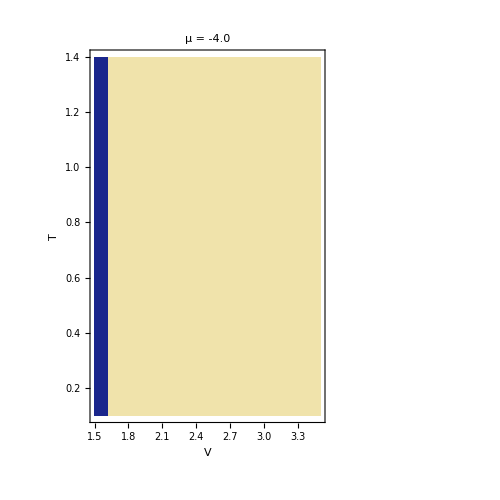

```mathematica
muFixed=-0.5;

Tmin=0.1;Tmax=1.4;nT=3;

VbisMin=1.5;VbisMax=3.5;nbis=2;
Vplotmin=1.5;Vplotmax=3.5;nV=8;

del=10^-3;mit=3;
ordCut=10^-3;

(*---Step 1:critical line Vc(T) by bisection at fixed mu---*)
For[iT=0,iT<=nT,iT++,T=Tmin+iT/nT (Tmax-Tmin);
mu=muFixed;
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
If[crit==1,v2=V,v1=V];];
tVal[iT]=T;
Vc[iT]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
tVals=Table[tVal[i],{i,0,nT}];
vcVals=Table[Vc[i],{i,0,nT}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with axes x=V,y=T---*)
phasePlotVT4=Flatten[Table[{vVals[[j+1]],tVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nT},{j,0,nV}],1];

critLineT=Table[{tVals[[i+1]],vcVals[[i+1]]},{i,0,nT}];
smooth=Interpolation[critLineT,InterpolationOrder->3];

tFine=Table[Tmin+s/400. (Tmax-Tmin),{s,0,400}];
smoothLine=Table[{smooth[t],t},{t,tFine}];

ListDensityPlot[phasePlotVT4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = -4.0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{21.5,0.45}],Text[Style["Disordered",16,Bold,White],{17.5,1.15}]}]
```